# Drift - time and Drift - length Simulation from 1 st principle

```mathematica
(* the accelration is depends on distance from wire or the driftlength *)
(* than we can calculation the drith-time and drift-length conversion *)
(* and we can discover the count on drifth -time is the differential conversion *)
```

```mathematica
(* assume the accelaration is *)
a[l_]:=-1/l
```

```mathematica
Integrate[-1/l,{l,L,d},Assumptions->{L>d>0}]
```

-Log[d/L]

```mathematica
Integrate[1/(√(2 Log[l/d])),{l,L,d},Assumptions->{L>d>0}]
```

-√2 L DawsonF[√Log[L/d]]

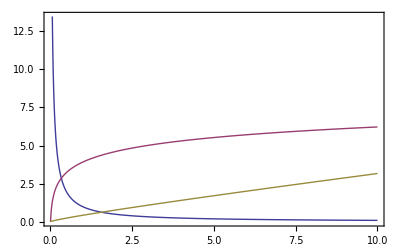

```mathematica
Plot[{1/L, Log[L/0.02],√2 L DawsonF[√Log[L/0.02]]},{L,0.02,10}, Frame->True]
```

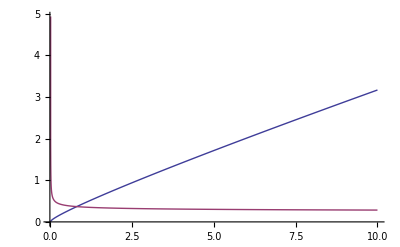

```mathematica
T[l_]:=√2 l DawsonF[√Log[l/0.02]]
DT[l_]:=D[T[y],y]/.y->l
Plot[{T[x],DT[x]},{x,0.02,10}]
```

## Simulation

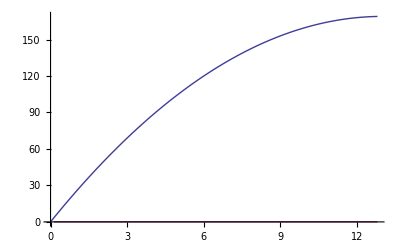

```mathematica
RangeX=√(8^2+10^2);
LCT[x_]:=If[RangeX>x>0,-(x-26)x,0]
DInvLCT[x_]:=D[InverseFunction[LCT][y],y]/.y->x
Plot[{LCT[x],DInvLCT[x]},{x,0,12.8}]
```

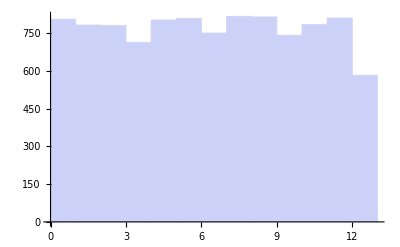

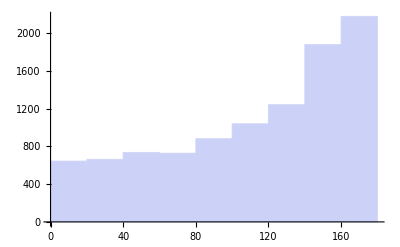

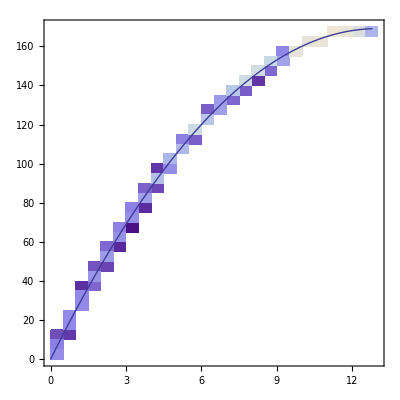

```mathematica
(* Generate random uniform even on 0.02 to 10 *)
n=10000;
DriftLengthList=Table[RandomReal[{0,RangeX}],{i,1,n}];
DriftTimeList=Table[LCT[DriftLengthList[[i]]],{i,1,n}];
DLDTList=Table[{DriftLengthList[[i]],DriftTimeList[[i]]},{i,1,n}];
Histogram[DriftLengthList,10]
Histogram[DriftTimeList,10]
Show[{
DensityHistogram[DLDTList,30],
Plot[{LCT[x]},{x,0,12.8}]
}]
```

### ConStructe The TCL from DriftTimeList

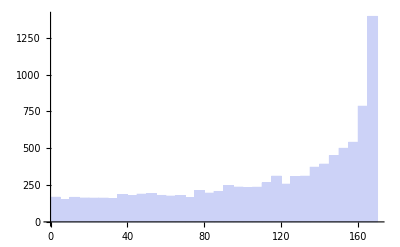

{{0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170},{167,150,166,162,161,161,157,184,178,188,191,179,175,178,165,210,195,206,246,236,232,235,264,310,256,307,310,371,392,450,499,540,785,1394}}

```mathematica
Histogram[DriftTimeList,30]
TempList=HistogramList[DriftTimeList,30]
```

```mathematica
DTCL=Table[{(TempList[[1,i]]+TempList[[1,i+1]])/2,TempList[[2,i]]},{i,1,34}]
```

{{5/2,167},{15/2,150},{25/2,166},{35/2,162},{45/2,161},{55/2,161},{65/2,157},{75/2,184},{85/2,178},{95/2,188},{105/2,191},{115/2,179},{125/2,175},{135/2,178},{145/2,165},{155/2,210},{165/2,195},{175/2,206},{185/2,246},{195/2,236},{205/2,232},{215/2,235},{225/2,264},{235/2,310},{245/2,256},{255/2,307},{265/2,310},{275/2,371},{285/2,392},{295/2,450},{305/2,499},{315/2,540},{325/2,785},{335/2,1394}}

```mathematica
DTCLConvertTCL[listx_]:=Module[{sumlist},
sumlist=Sum[listx[[i,2]],{i,1,Length[listx]}];
Table[{listx[[i,1]],Sum[listx[[j,2]],{j,1,i}]/sumlist RangeX},{i,1,Length[listx]}]
]
```

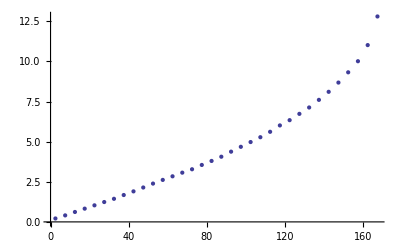

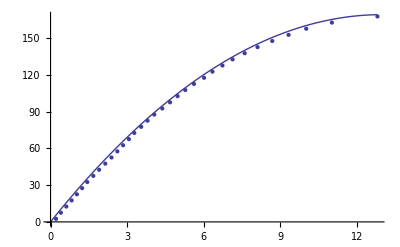

```mathematica
TCL=DTCLConvertTCL[DTCL]//N;
ListPlot[TCL]
LCTβ=Table[{TCL[[i,2]],TCL[[i,1]]},{i,1,Length[TCL]}];
Show[{
ListPlot[LCTβ],
Plot[{LCT[x]},{x,0,12.8}]
}]
```

## From Drift time PAW Vector

```mathematica
binSize[int_,end_,binNum_]:=(end-int)/binNum//N
binList[int_,end_,binNum_,center_]:=If[center,
Table[int+(i+1/2) binSize[int,end,binNum],{i,0,binNum-1}],
Table[int+i binSize[int,end,binNum],{i,0,binNum-1}]]
```

```mathematica
Solve[binSize[-141.6,106.4,x]==0.4,x]
binList[-141.6,106.4,620,True];
Length[%]
```

{{x→620.}}

620

```mathematica
Directory[]
```

C:\Users\Ryan\Documents

```mathematica
Export["dt_x1.dat",binList[-141.6,106.4,620,True]]
```

dt_x1.dat